We define the following kinetics for the metabolic enzymes in the pathway

```mathematica
rateeqs={vhill->((v1f*s)/s05(1-x1[t]/(s Keq1))(s/s05+x1[t]/x1105)^(n-1))/((s/s05+x1[t]/x1105)^n+(1+(x3/x3105)^n)/(1+α(x3/x3105)^n)),
v2->(1000(x1[t]-x2[t]/10))/(1+x1[t]+x2[t]),
v3->(1000(x2[t]-x3/10))/(1+x1[t]+x2[t]),
v4->(10x3)/(0.01+x3)};
parm={s->1, Keq1->400, x1105->10^4, n->4, x3105->1,α->0.001,s05->1};
odes={
x1'[t]==vhill-v2,
x2'[t]==v2-v3};
vars={x1,x2};
init={x1[0]==10,x2[0]==20};
```

The first enzyme was made insensitive to it's immediate product x1 by making its Km high, i.e. 10^4

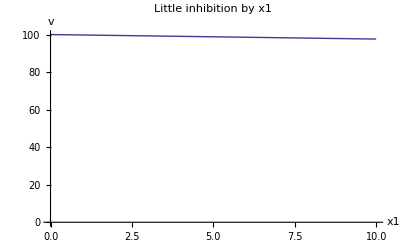

```mathematica
Plot[vhill/.rateeqs/.parm/.x3->0/.v1f->200,{x1[t],0,10},PlotRange->{{0,10},{0,100}},PlotLabel->"Little inhibition by x1",AxesLabel->{"x1","v"}]
```

The first enzyme in the absence of feedback not determines largely the flux because its acts as a pump as the feedback of it's product is negligible.

The pathway operates at equilibrium when

P/S=K_EQ1 K_EQ2 K_EQ3=400 10 10=40000
Given that s=1 if p=40000 then pathway is in equilibrium and 
x1/s=400, x2/x1=10, x3/x2=10

Let's check

```mathematica
{vhill,v2,v3}/.rateeqs/.parm/.x1[t]->400/.x2[t]->4000/.x3->40000
```

{0,0,0}

And indeed with those concentration the pathway rates are zero!

To analyse the steady state behavior of this pathway, we need to start with a time dependent solution as an initial guess for the calculation of the steady state

```mathematica
tsol[x3val_,V1fval_]:=NDSolve[Join[odes/.rateeqs/.parm/.x3->x3val/.v1f->V1fval,init],vars,{t,0,100}]
```

The steady state can then be calculated by,

```mathematica
ss[x3val_,V1fval_]:=FindRoot[Table[(odes[[i]][[2]]==0)/.rateeqs/.parm/.x3->x3val/.v1f->V1fval,{i,1,Length[odes]}],Table[{vars[[i]][t],(vars[[i]][100]/.tsol[x3val,V1fval])[[1]]},{i,1,Length[vars]}]]
```

A test calculation shows indeed all the odes are zero in the steady

```mathematica
ss[1,200]
odes/.rateeqs/.parm/.x3->1/.v1f->200/.%
```

{x1[t]→0.104698,x2[t]→0.186089}

{x1'[t]==-1.42109×10^-14,x2'[t]==0.}

We can now calculate the steady state flux as function of x3

```mathematica
ssrange[v1fval_]:=Table[{x3val,vhill/.rateeqs/.parm/.x3->x3val/.v1f->v1fval/.ss[x3val,v1fval]},{x3val,{0,0.01,0.1,0.25,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,2,3,4,5,6,7,8,9,10,20,30,40,60,100,200,300,400,500,600,700,800,900,1000,2000,3000,5000,7500,10000,15000,20000,25000,30000,40000}}];
```

The error messages below are do not matter!

```mathematica
ssdat1=ssrange[50];
ssdat2=ssrange[75];
ssdat3=ssrange[100];
ssdat4=ssrange[150];
ssdat5=ssrange[200];
ssdat6=ssrange[500];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

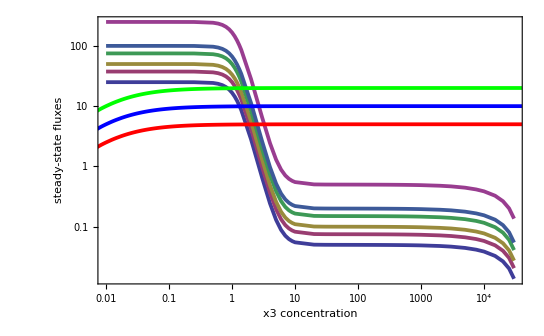

```mathematica
Show[{ListLogLogPlot[{ssdat1,ssdat2,ssdat3,ssdat4,ssdat5,ssdat6},Joined->True,Frame->True,FrameLabel->{"x3 concentration","steady-state fluxes"},BaseStyle->{FontFamily->"Gill Sans Light",FontSize->16},PlotStyle->Thickness[.005],PlotRange->{{0,40000},All}],
LogLogPlot[{(5x3)/(0.01+x3),(10x3)/(0.01+x3),(20x3)/(0.01+x3)},{x3,0.001,40000},PlotStyle->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]},{Green,Thickness[0.005]}}]}]
```

The red line is the consumption reaction rate of metabolite, X3, catalyzed by reaction 4.  The others differ in the maximal rate of the first reaction and each give the steady-state flux through the metabolic module composed out of the first three enzymes - the supply module.  The higher lines have a higher value for this maximal rate  If the intersection of the red line and rate curve for the supply module lies in the decreasing segment of the supply rate curve, a change in maximal rate of the fourth enzyme (the red, blue, and green curve) brings about a large change in the steady-state flux, the intersection point; a change in the Vmax of the first enzyme does not change the steady-state flux (the other lines).

The fourth enzyme has the largest effect on the flux.
Playing with s05 will shift the rate curve of the supply module.
The strength of the feedback, n and x1305, change the sigmoidality properties of this rate curve.
All of this you can check with this notebook.

If the supply rate curve is steep when the demand rate, enzyme 4, intersect it then a large change in the flux can be obtained when the change in the concentration of the feedback metabolite, x3, is only little.  This is called homeostasis.

When a feedback strongly inhibits a synthesis pathway the control on the flux shift to the reactions after the feebdback metabolite. This metabolite remains homeostatic when flux changes are brought about by modulation of the level of the enzymes after the feedback metabolite.